# Genetic Evolution of Wolfram Models

The idea is to use genetic evolution to modify rules for a Wolfram Model to satisfy an objective. This means starting from a rule and performing mutation and crossover on individual replacements to build up a more complex rule. The population can be managed based on any kind of objective function.

## Initial Tests

```mathematica
wm=ResourceFunction["WolframModel"];
plot=ResourceFunction["WolframModelPlot"];
```

```mathematica
(* random initial rule *)
signature = {{2,2}}->{{5,2}};
rule = ResourceFunction["RandomWolframModel"][signature]
```

{{1,2},{2,3}}→{{4,1},{4,1},{4,3},{1,5},{5,3}}

```mathematica
steps=10;
init={{1,1},{1,1}};
```

```mathematica
final=wm[rule, init, steps, "FinalState"]
```

{{10,4},{10,4},{10,1},{36,18},{36,18},{36,1},{44,20},{44,20},{44,3},{100,54},{100,54},{100,15},{134,68},{134,68},{134,1},{142,70},{142,70},{142,11},{160,76},{160,76},{160,3},{168,78},{168,78},{168,13},{300,1},{301,1},{302,172},{302,1},{303,1},{304,172},{304,172},{305,173},{306,1},{307,1},{308,174},{309,175},{310,48},{311,48},{312,176},{312,48},{313,48},{314,84},{314,23},{315,23},{316,48},{317,48},{318,178},{318,1},{319,1},{320,178},{320,178},{320,49},{321,49},{322,82},{322,85},{323,85},{324,1},{325,1},{326,180},{327,181},{328,1},{329,1},{330,182},{331,183},{332,50},{333,50},{334,184},{335,185},{336,51},{337,51},{338,186},{339,187},{340,14},{341,14},{342,188},{343,189},{344,14},{345,14},{346,190},{347,191},{348,52},{349,52},{350,192},{350,14},{351,14},{352,192},{352,192},{352,14},{353,14},{354,92},{354,93},{355,93},{356,26},{357,26},{358,194},{358,7},{359,7},{360,194},{360,194},{360,7},{361,7},{362,94},{362,95},{363,95},{364,14},{365,14},{366,196},{366,14},{367,14},{368,196},{368,196},{369,197},{370,1},{371,1},{372,198},{373,199},{374,54},{375,54},{376,200},{376,1},{377,1},{378,200},{378,200},{378,15},{379,15},{380,98},{380,101},{381,101},{382,24},{383,24},{384,202},{384,27},{385,27},{386,202},{386,202},{386,27},{387,27},{388,102},{388,103},{389,103},{390,1},{391,1},{392,204},{393,205},{394,1},{395,1},{396,206},{397,207},{398,56},{399,56},{400,208},{401,209},{402,57},{403,57},{404,210},{405,211},{406,1},{407,1},{408,212},{409,213},{410,1},{411,1},{412,214},{413,215},{414,58},{415,58},{416,216},{417,217},{418,59},{419,59},{420,218},{421,219},{422,16},{423,16},{424,220},{425,221},{426,16},{427,16},{428,222},{429,223},{430,60},{431,60},{432,224},{433,225},{434,61},{435,61},{436,226},{437,227},{438,17},{439,17},{440,228},{441,229},{442,17},{443,17},{444,230},{445,231},{446,62},{447,62},{448,232},{449,233},{450,63},{451,63},{452,234},{453,235},{454,4},{455,4},{456,236},{456,4},{457,4},{458,236},{458,236},{459,237},{460,4},{461,4},{462,238},{463,239},{464,64},{465,64},{466,240},{466,64},{467,64},{468,124},{468,33},{469,33},{470,64},{471,64},{472,242},{472,4},{473,4},{474,242},{474,242},{474,65},{475,65},{476,122},{476,125},{477,125},{478,1},{479,1},{480,244},{481,245},{482,1},{483,1},{484,246},{485,247},{486,66},{487,66},{488,248},{489,249},{490,67},{491,67},{492,250},{493,251},{494,18},{495,18},{496,252},{496,18},{497,18},{498,252},{498,252},{499,253},{500,1},{501,1},{502,254},{503,255},{504,68},{505,68},{506,256},{506,1},{507,1},{508,256},{508,256},{508,1},{509,1},{510,132},{510,135},{511,135},{512,34},{513,34},{514,258},{514,37},{515,37},{516,258},{516,258},{516,37},{517,37},{518,136},{518,137},{519,137},{520,8},{521,8},{522,260},{522,8},{523,8},{524,260},{524,260},{525,261},{526,11},{527,11},{528,262},{529,263},{530,70},{531,70},{532,264},{532,11},{533,11},{534,264},{534,264},{534,11},{535,11},{536,140},{536,143},{537,143},{538,38},{539,38},{540,266},{540,39},{541,39},{542,266},{542,266},{542,39},{543,39},{544,144},{544,145},{545,145},{546,2},{547,2},{548,268},{548,2},{549,2},{550,268},{550,268},{551,269},{552,2},{553,2},{554,270},{555,271},{556,72},{557,72},{558,272},{558,72},{559,72},{560,150},{560,41},{561,41},{562,72},{563,72},{564,274},{564,2},{565,2},{566,274},{566,274},{566,73},{567,73},{568,148},{568,151},{569,151},{570,3},{571,3},{572,276},{573,277},{574,3},{575,3},{576,278},{577,279},{578,74},{579,74},{580,280},{581,281},{582,75},{583,75},{584,282},{585,283},{586,20},{587,20},{588,284},{588,20},{589,20},{590,284},{590,284},{591,285},{592,3},{593,3},{594,286},{595,287},{596,76},{597,76},{598,288},{598,3},{599,3},{600,288},{600,288},{600,3},{601,3},{602,158},{602,161},{603,161},{604,42},{605,42},{606,290},{606,45},{607,45},{608,290},{608,290},{608,45},{609,45},{610,162},{610,163},{611,163},{612,12},{613,12},{614,292},{614,12},{615,12},{616,292},{616,292},{617,293},{618,13},{619,13},{620,294},{621,295},{622,78},{623,78},{624,296},{624,13},{625,13},{626,296},{626,296},{626,13},{627,13},{628,166},{628,169},{629,169},{630,46},{631,46},{632,298},{632,47},{633,47},{634,298},{634,298},{634,47},{635,47},{636,170},{636,171},{637,171},{638,300},{638,300},{638,301},{300,639},{639,301},{640,300},{640,300},{640,303},{300,641},{641,303},{642,304},{642,304},{642,81},{304,643},{643,81},{644,302},{644,302},{644,305},{302,645},{645,305},{646,306},{646,306},{646,80},{306,647},{647,80},{648,306},{648,306},{648,307},{306,649},{649,307},{650,308},{650,308},{650,83},{308,651},{651,83},{652,308},{652,308},{652,309},{308,653},{653,309},{654,310},{654,310},{654,23},{310,655},{655,23},{656,310},{656,310},{656,311},{310,657},{657,311},{658,312},{658,312},{658,313},{312,659},{659,313},{660,314},{660,314},{660,315},{314,661},{661,315},{662,316},{662,316},{662,317},{316,663},{663,317},{664,316},{664,316},{664,319},{316,665},{665,319},{666,318},{666,318},{666,321},{318,667},{667,321},{668,322},{668,322},{668,323},{322,669},{669,323},{670,324},{670,324},{670,22},{324,671},{671,22},{672,324},{672,324},{672,325},{324,673},{673,325},{674,326},{674,326},{674,22},{326,675},{675,22},{676,326},{676,326},{676,327},{326,677},{677,327},{678,328},{678,328},{678,86},{328,679},{679,86},{680,328},{680,328},{680,329},{328,681},{681,329},{682,330},{682,330},{682,87},{330,683},{683,87},{684,330},{684,330},{684,331},{330,685},{685,331},{686,332},{686,332},{686,25},{332,687},{687,25},{688,332},{688,332},{688,333},{332,689},{689,333},{690,334},{690,334},{690,25},{334,691},{691,25},{692,334},{692,334},{692,335},{334,693},{693,335},{694,336},{694,336},{694,88},{336,695},{695,88},{696,336},{696,336},{696,337},{336,697},{697,337},{698,338},{698,338},{698,89},{338,699},{699,89},{700,338},{700,338},{700,339},{338,701},{701,339},{702,340},{702,340},{702,7},{340,703},{703,7},{704,340},{704,340},{704,341},{340,705},{705,341},{706,342},{706,342},{706,7},{342,707},{707,7},{708,342},{708,342},{708,343},{342,709},{709,343},{710,344},{710,344},{710,90},{344,711},{711,90},{712,344},{712,344},{712,345},{344,713},{713,345},{714,346},{714,346},{714,91},{346,715},{715,91},{716,346},{716,346},{716,347},{346,717},{717,347},{718,348},{718,348},{718,349},{348,719},{719,349},{720,348},{720,348},{720,351},{348,721},{721,351},{722,350},{722,350},{722,353},{350,723},{723,353},{724,354},{724,354},{724,355},{354,725},{725,355},{726,356},{726,356},{726,357},{356,727},{727,357},{728,356},{728,356},{728,359},{356,729},{729,359},{730,358},{730,358},{730,361},{358,731},{731,361},{732,362},{732,362},{732,363},{362,733},{733,363},{734,364},{734,364},{734,365},{364,735},{735,365},{736,364},{736,364},{736,367},{364,737},{737,367},{738,368},{738,368},{738,97},{368,739},{739,97},{740,366},{740,366},{740,369},{366,741},{741,369},{742,370},{742,370},{742,96},{370,743},{743,96},{744,370},{744,370},{744,371},{370,745},{745,371},{746,372},{746,372},{746,99},{372,747},{747,99},{748,372},{748,372},{748,373},{372,749},{749,373},{750,374},{750,374},{750,375},{374,751},{751,375},{752,374},{752,374},{752,377},{374,753},{753,377},{754,376},{754,376},{754,379},{376,755},{755,379},{756,380},{756,380},{756,381},{380,757},{757,381},{758,382},{758,382},{758,383},{382,759},{759,383},{760,382},{760,382},{760,385},{382,761},{761,385},{762,384},{762,384},{762,387},{384,763},{763,387},{764,388},{764,388},{764,389},{388,765},{765,389},{766,390},{766,390},{766,6},{390,767},{767,6},{768,390},{768,390},{768,391},{390,769},{769,391},{770,392},{770,392},{770,6},{392,771},{771,6},{772,392},{772,392},{772,393},{392,773},{773,393},{774,394},{774,394},{774,104},{394,775},{775,104},{776,394},{776,394},{776,395},{394,777},{777,395},{778,396},{778,396},{778,105},{396,779},{779,105},{780,396},{780,396},{780,397},{396,781},{781,397},{782,398},{782,398},{782,6},{398,783},{783,6},{784,398},{784,398},{784,399},{398,785},{785,399},{786,400},{786,400},{786,6},{400,787},{787,6},{788,400},{788,400},{788,401},{400,789},{789,401},{790,402},{790,402},{790,106},{402,791},{791,106},{792,402},{792,402},{792,403},{402,793},{793,403},{794,404},{794,404},{794,107},{404,795},{795,107},{796,404},{796,404},{796,405},{404,797},{797,405},{798,406},{798,406},{798,28},{406,799},{799,28},{800,406},{800,406},{800,407},{406,801},{801,407},{802,408},{802,408},{802,28},{408,803},{803,28},{804,408},{804,408},{804,409},{408,805},{805,409},{806,410},{806,410},{806,108},{410,807},{807,108},{808,410},{808,410},{808,411},{410,809},{809,411},{810,412},{810,412},{810,109},{412,811},{811,109},{812,412},{812,412},{812,413},{412,813},{813,413},{814,414},{814,414},{814,29},{414,815},{815,29},{816,414},{816,414},{816,415},{414,817},{817,415},{818,416},{818,416},{818,29},{416,819},{819,29},{820,416},{820,416},{820,417},{416,821},{821,417},{822,418},{822,418},{822,110},{418,823},{823,110},{824,418},{824,418},{824,419},{418,825},{825,419},{826,420},{826,420},{826,111},{420,827},{827,111},{828,420},{828,420},{828,421},{420,829},{829,421},{830,422},{830,422},{830,9},{422,831},{831,9},{832,422},{832,422},{832,423},{422,833},{833,423},{834,424},{834,424},{834,9},{424,835},{835,9},{836,424},{836,424},{836,425},{424,837},{837,425},{838,426},{838,426},{838,112},{426,839},{839,112},{840,426},{840,426},{840,427},{426,841},{841,427},{842,428},{842,428},{842,113},{428,843},{843,113},{844,428},{844,428},{844,429},{428,845},{845,429},{846,430},{846,430},{846,9},{430,847},{847,9},{848,430},{848,430},{848,431},{430,849},{849,431},{850,432},{850,432},{850,9},{432,851},{851,9},{852,432},{852,432},{852,433},{432,853},{853,433},{854,434},{854,434},{854,114},{434,855},{855,114},{856,434},{856,434},{856,435},{434,857},{857,435},{858,436},{858,436},{858,115},{436,859},{859,115},{860,436},{860,436},{860,437},{436,861},{861,437},{862,438},{862,438},{862,30},{438,863},{863,30},{864,438},{864,438},{864,439},{438,865},{865,439},{866,440},{866,440},{866,30},{440,867},{867,30},{868,440},{868,440},{868,441},{440,869},{869,441},{870,442},{870,442},{870,116},{442,871},{871,116},{872,442},{872,442},{872,443},{442,873},{873,443},{874,444},{874,444},{874,117},{444,875},{875,117},{876,444},{876,444},{876,445},{444,877},{877,445},{878,446},{878,446},{878,31},{446,879},{879,31},{880,446},{880,446},{880,447},{446,881},{881,447},{882,448},{882,448},{882,31},{448,883},{883,31},{884,448},{884,448},{884,449},{448,885},{885,449},{886,450},{886,450},{886,118},{450,887},{887,118},{888,450},{888,450},{888,451},{450,889},{889,451},{890,452},{890,452},{890,119},{452,891},{891,119},{892,452},{892,452},{892,453},{452,893},{893,453},{894,454},{894,454},{894,455},{454,895},{895,455},{896,454},{896,454},{896,457},{454,897},{897,457},{898,458},{898,458},{898,121},{458,899},{899,121},{900,456},{900,456},{900,459},{456,901},{901,459},{902,460},{902,460},{902,120},{460,903},{903,120},{904,460},{904,460},{904,461},{460,905},{905,461},{906,462},{906,462},{906,123},{462,907},{907,123},{908,462},{908,462},{908,463},{462,909},{909,463},{910,464},{910,464},{910,33},{464,911},{911,33},{912,464},{912,464},{912,465},{464,913},{913,465},{914,466},{914,466},{914,467},{466,915},{915,467},{916,468},{916,468},{916,469},{468,917},{917,469},{918,470},{918,470},{918,471},{470,919},{919,471},{920,470},{920,470},{920,473},{470,921},{921,473},{922,472},{922,472},{922,475},{472,923},{923,475},{924,476},{924,476},{924,477},{476,925},{925,477},{926,478},{926,478},{926,32},{478,927},{927,32},{928,478},{928,478},{928,479},{478,929},{929,479},{930,480},{930,480},{930,32},{480,931},{931,32},{932,480},{932,480},{932,481},{480,933},{933,481},{934,482},{934,482},{934,126},{482,935},{935,126},{936,482},{936,482},{936,483},{482,937},{937,483},{938,484},{938,484},{938,127},{484,939},{939,127},{940,484},{940,484},{940,485},{484,941},{941,485},{942,486},{942,486},{942,35},{486,943},{943,35},{944,486},{944,486},{944,487},{486,945},{945,487},{946,488},{946,488},{946,35},{488,947},{947,35},{948,488},{948,488},{948,489},{488,949},{949,489},{950,490},{950,490},{950,128},{490,951},{951,128},{952,490},{952,490},{952,491},{490,953},{953,491},{954,492},{954,492},{954,129},{492,955},{955,129},{956,492},{956,492},{956,493},{492,957},{957,493},{958,494},{958,494},{958,495},{494,959},{959,495},{960,494},{960,494},{960,497},{494,961},{961,497},{962,498},{962,498},{962,131},{498,963},{963,131},{964,496},{964,496},{964,499},{496,965},{965,499},{966,500},{966,500},{966,130},{500,967},{967,130},{968,500},{968,500},{968,501},{500,969},{969,501},{970,502},{970,502},{970,133},{502,971},{971,133},{972,502},{972,502},{972,503},{502,973},{973,503},{974,504},{974,504},{974,505},{504,975},{975,505},{976,504},{976,504},{976,507},{504,977},{977,507},{978,506},{978,506},{978,509},{506,979},{979,509},{980,510},{980,510},{980,511},{510,981},{981,511},{982,512},{982,512},{982,513},{512,983},{983,513},{984,512},{984,512},{984,515},{512,985},{985,515},{986,514},{986,514},{986,517},{514,987},{987,517},{988,518},{988,518},{988,519},{518,989},{989,519},{990,520},{990,520},{990,521},{520,991},{991,521},{992,520},{992,520},{992,523},{520,993},{993,523},{994,524},{994,524},{994,139},{524,995},{995,139},{996,522},{996,522},{996,525},{522,997},{997,525},{998,526},{998,526},{998,138},{526,999},{999,138},{1000,526},{1000,526},{1000,527},{526,1001},{1001,527},{1002,528},{1002,528},{1002,141},{528,1003},{1003,141},{1004,528},{1004,528},{1004,529},{528,1005},{1005,529},{1006,530},{1006,530},{1006,531},{530,1007},{1007,531},{1008,530},{1008,530},{1008,533},{530,1009},{1009,533},{1010,532},{1010,532},{1010,535},{532,1011},{1011,535},{1012,536},{1012,536},{1012,537},{536,1013},{1013,537},{1014,538},{1014,538},{1014,539},{538,1015},{1015,539},{1016,538},{1016,538},{1016,541},{538,1017},{1017,541},{1018,540},{1018,540},{1018,543},{540,1019},{1019,543},{1020,544},{1020,544},{1020,545},{544,1021},{1021,545},{1022,546},{1022,546},{1022,547},{546,1023},{1023,547},{1024,546},{1024,546},{1024,549},{546,1025},{1025,549},{1026,550},{1026,550},{1026,147},{550,1027},{1027,147},{1028,548},{1028,548},{1028,551},{548,1029},{1029,551},{1030,552},{1030,552},{1030,146},{552,1031},{1031,146},{1032,552},{1032,552},{1032,553},{552,1033},{1033,553},{1034,554},{1034,554},{1034,149},{554,1035},{1035,149},{1036,554},{1036,554},{1036,555},{554,1037},{1037,555},{1038,556},{1038,556},{1038,41},{556,1039},{1039,41},{1040,556},{1040,556},{1040,557},{556,1041},{1041,557},{1042,558},{1042,558},{1042,559},{558,1043},{1043,559},{1044,560},{1044,560},{1044,561},{560,1045},{1045,561},{1046,562},{1046,562},{1046,563},{562,1047},{1047,563},{1048,562},{1048,562},{1048,565},{562,1049},{1049,565},{1050,564},{1050,564},{1050,567},{564,1051},{1051,567},{1052,568},{1052,568},{1052,569},{568,1053},{1053,569},{1054,570},{1054,570},{1054,40},{570,1055},{1055,40},{1056,570},{1056,570},{1056,571},{570,1057},{1057,571},{1058,572},{1058,572},{1058,40},{572,1059},{1059,40},{1060,572},{1060,572},{1060,573},{572,1061},{1061,573},{1062,574},{1062,574},{1062,152},{574,1063},{1063,152},{1064,574},{1064,574},{1064,575},{574,1065},{1065,575},{1066,576},{1066,576},{1066,153},{576,1067},{1067,153},{1068,576},{1068,576},{1068,577},{576,1069},{1069,577},{1070,578},{1070,578},{1070,43},{578,1071},{1071,43},{1072,578},{1072,578},{1072,579},{578,1073},{1073,579},{1074,580},{1074,580},{1074,43},{580,1075},{1075,43},{1076,580},{1076,580},{1076,581},{580,1077},{1077,581},{1078,582},{1078,582},{1078,154},{582,1079},{1079,154},{1080,582},{1080,582},{1080,583},{582,1081},{1081,583},{1082,584},{1082,584},{1082,155},{584,1083},{1083,155},{1084,584},{1084,584},{1084,585},{584,1085},{1085,585},{1086,586},{1086,586},{1086,587},{586,1087},{1087,587},{1088,586},{1088,586},{1088,589},{586,1089},{1089,589},{1090,590},{1090,590},{1090,157},{590,1091},{1091,157},{1092,588},{1092,588},{1092,591},{588,1093},{1093,591},{1094,592},{1094,592},{1094,156},{592,1095},{1095,156},{1096,592},{1096,592},{1096,593},{592,1097},{1097,593},{1098,594},{1098,594},{1098,159},{594,1099},{1099,159},{1100,594},{1100,594},{1100,595},{594,1101},{1101,595},{1102,596},{1102,596},{1102,597},{596,1103},{1103,597},{1104,596},{1104,596},{1104,599},{596,1105},{1105,599},{1106,598},{1106,598},{1106,601},{598,1107},{1107,601},{1108,602},{1108,602},{1108,603},{602,1109},{1109,603},{1110,604},{1110,604},{1110,605},{604,1111},{1111,605},{1112,604},{1112,604},{1112,607},{604,1113},{1113,607},{1114,606},{1114,606},{1114,609},{606,1115},{1115,609},{1116,610},{1116,610},{1116,611},{610,1117},{1117,611},{1118,612},{1118,612},{1118,613},{612,1119},{1119,613},{1120,612},{1120,612},{1120,615},{612,1121},{1121,615},{1122,616},{1122,616},{1122,165},{616,1123},{1123,165},{1124,614},{1124,614},{1124,617},{614,1125},{1125,617},{1126,618},{1126,618},{1126,164},{618,1127},{1127,164},{1128,618},{1128,618},{1128,619},{618,1129},{1129,619},{1130,620},{1130,620},{1130,167},{620,1131},{1131,167},{1132,620},{1132,620},{1132,621},{620,1133},{1133,621},{1134,622},{1134,622},{1134,623},{622,1135},{1135,623},{1136,622},{1136,622},{1136,625},{622,1137},{1137,625},{1138,624},{1138,624},{1138,627},{624,1139},{1139,627},{1140,628},{1140,628},{1140,629},{628,1141},{1141,629},{1142,630},{1142,630},{1142,631},{630,1143},{1143,631},{1144,630},{1144,630},{1144,633},{630,1145},{1145,633},{1146,632},{1146,632},{1146,635},{632,1147},{1147,635},{1148,636},{1148,636},{1148,637},{636,1149},{1149,637}}

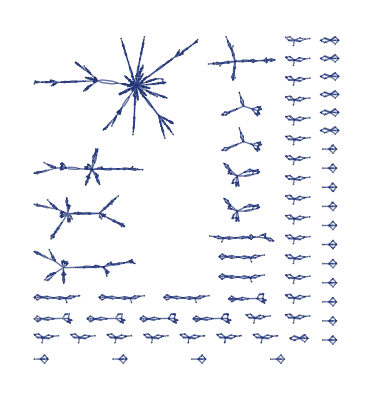

```mathematica
plot[final]
```

## Possible Mutations

Insertion

Add new transformation of simple signature

Add new transformation of random signature

Add new transformation of signature which can apply

Deletion

Remove replacement entirely

Remove one piece of rhs or lhs

Remove one element in a relation

Modification

Swap one full replacement for a random one

Swap one element in a replacement (either side)

Add one element to a replacement (either side)

## Rule Mutation

#### Generation

```mathematica
generateRandomRule[maxRelations_, maxElements_, maxPieces_] := 
	ResourceFunction["RandomWolframModel"][
		generateRandomSignature[maxRelations, maxElements, maxPieces]
	] // List // Flatten
	
generateRandomSignature[maxRelations_, maxElements_, maxPieces_] := 
	Rule @@ Table[
		Table[
			{RandomInteger[{1, maxRelations}], RandomInteger[{1, maxElements}]},
			RandomInteger[{1, maxPieces}]
		], 
		2
	]
	
generateRandomRelation[elementRange_List, nElementsRange_List] := 
	RandomInteger[elementRange, RandomInteger[nElementsRange]]
```

#### Selection

```mathematica
chooseRandomRelation[rule_] :=
	With[{
			replacement = RandomInteger[{1, Length @ rule}],
			side = RandomInteger[{1, 2}]
		},
		{replacement, side, RandomInteger[{1, Length @ rule[[replacement, side]]}]}
	]
```

#### Insertion

```mathematica
insertTrivialReplacement[rule_] := 
	Append[rule, {{1, 1}} -> {{1, 1}}]
		
insertRandomReplacement[rule_, maxRelations_, maxElements_, maxPieces_] := 
	Append[rule, 
		ResourceFunction["RandomWolframModel"][
			generateRandomSignature[maxRelations, maxElements, maxPieces]
		]
	]

(*	
insertRandomRelation[rule_, elementRange_List, nElementsRange_List] :=
	With[{relation = chooseRandomRelation[rule]},
		ReplacePart[rule, relation -> Sequence[
			rule[[Sequence @@ relation]], generateRandomRelation[elementRange, nElementsRange]
		]]
	]
*)
	
insertRandomRelation[rule_, elementRange_List, nElementsRange_List] :=
	With[{relation = chooseRandomRelation[rule]},
		ReplacePart[rule, relation -> generateRandomRelation[elementRange, nElementsRange]
		]
	]
	
insertRandomElement[rule_] := Nothing
```

```mathematica
signature = {{2,2}}->{{3,2}};
rule = ResourceFunction["RandomWolframModel"][signature]
```

{{1,2},{1,3}}→{{4,2},{2,3},{1,5}}

```mathematica
insertRandomRelation[rule, {1,5}, {1,3}]
```

{{1,2},{1,3}}→{{{3,2},2},{2,3},{1,5}}

```mathematica
ResourceFunction["EnumerateWolframModelRules"][{{2,2}}->{{3,2}}]
```

OptionValue::nodef: Unknown option ProgressReporting for ParallelMap.

{{{1,1},{1,1}}→{{1,1},{1,1},{1,1}},{{1,1},{1,1}}→{{1,1},{1,1},{1,2}},{{1,1},{1,1}}→{{1,1},{1,1},{2,1}},{{1,1},{1,1}}→{{1,1},{1,2},{1,2}},{{1,1},{1,1}}→{{1,1},{1,2},{2,1}},{{1,1},{1,1}}→{{1,1},{1,2},{2,2}},{{1,1},{1,1}}→{{1,1},{1,2},{1,3}},{{1,1},{1,1}}→{{1,1},{1,2},{2,3}},{{1,1},{1,1}}→{{1,1},{1,2},{3,1}},4685,{{1,2},{3,2}}→{{4,5},{4,6},{2,4}},{{1,2},{3,2}}→{{4,5},{4,6},{2,5}},{{1,2},{3,2}}→{{4,5},{4,6},{5,1}},{{1,2},{3,2}}→{{4,5},{4,6},{5,2}},{{1,2},{3,2}}→{{4,5},{5,6},{1,6}},{{1,2},{3,2}}→{{4,5},{5,6},{2,6}},{{1,2},{3,2}}→{{4,5},{5,6},{6,1}},{{1,2},{3,2}}→{{4,5},{5,6},{6,2}}}
 |  |  |  |

```mathematica
ResourceFunction["EnumerateWolframModelRules"][{{1,2}}->{{1,2}}]
```

ResourceFunction::usermessage: ParallelMapMonitored

OptionValue::nodef: Unknown option ProgressReporting for ParallelMap.

{{{1,1}}→{{1,1}},{{1,1}}→{{1,2}},{{1,1}}→{{2,1}},{{1,2}}→{{1,1}},{{1,2}}→{{1,2}},{{1,2}}→{{2,1}},{{1,2}}→{{2,2}},{{1,2}}→{{1,3}},{{1,2}}→{{2,3}},{{1,2}}→{{3,1}},{{1,2}}→{{3,2}}}

#### Deletion

```mathematica
deleteRandomReplacement[rule_] :=
	Delete[
		rule,
		RandomInteger[{1, Length[rule]}]
	]

deleteRandomRelation[rule_] :=
	Delete[rule, chooseRandomRelation[rule]]
	
deleteRandomElement[rule_] := Nothing
```

#### Replacement

```mathematica
replaceRandomRelation[rule_, elementRange_List, nElementsRange_List] := 
	With[{
			replacement = RandomInteger[{1, Length @ rule}],
			side = RandomInteger[{1, 2}]
		},
		ReplacePart[rule, {replacement, side, RandomInteger[{1, Length @ rule[[replacement, side]]}]} -> 
			generateRandomRelation[elementRange, nElementsRange]
		]
	]
```

#### Utility

```mathematica
relationSignature[relation_] := 
	List@@Reverse[#] & /@ Normal[Counts[Length /@ relation]]
	
ruleSignature[rule_] :=
	Map[relationSignature[First @ #] -> relationSignature[Last @ #] &, rule]
```

#### Target Function

```mathematica
graphDimension[graph_] := 
	ResourceFunction["WolframHausdorffDimension"][Graph[graph], All, "VertexMethod" -> Max]
```

```mathematica
rule
```

{{1,2},{1,3}}→{{4,2},{4,3},{2,1}}

```mathematica
elementRange = {1,5};
nElementsRange = {1,3};
nRules = 3;
```

```mathematica
ruleInsertions =Table[insertRandomRelation[rule, elementRange, nElementsRange], nRules]
```

{{{1,2},{1,3}}→{{4,2,{1,4,5}},{4,3},{2,1}},{{1,2},{1,{2,4,2},3}}→{{4,2},{4,3},{2,1}},{{1,2},{1,3,{3}}}→{{4,2},{4,3},{2,1}}}

```mathematica
ruleDeletions = Table[deleteRandomRelation[rule], nRules]
```

{{{1,2},{1,3}}→{{4,2},{3},{2,1}},{{1,2},{1,3}}→{{2},{4,3},{2,1}},{{1,2},{1}}→{{4,2},{4,3},{2,1}}}

```mathematica
ruleReplacements = Table[replaceRandomRelation[rule, elementRange, nElementsRange], nRules]
```

{{{{3,3,1},2},{1,3}}→{{4,2},{4,3},{2,1}},{{1,2},{1,3}}→{{4,2},{{3,1,5},3},{2,1}},{{1,2},{1,3}}→{{{4,3,2},2},{4,3},{2,1}}}

```mathematica
allRules = Flatten[Join[ruleInsertions,ruleDeletions,ruleReplacements],1];
```

Transpose::nmtx: The first two levels of … cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::nmtx: The first two levels of … cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

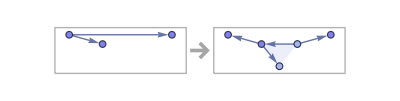
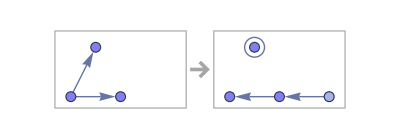
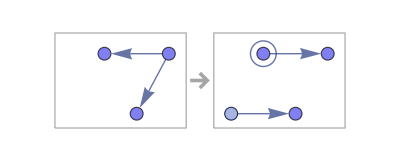
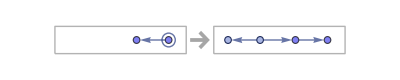
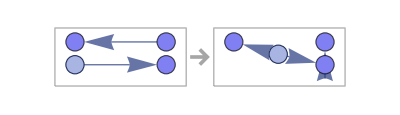
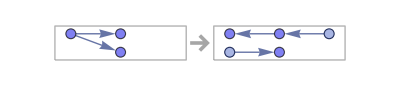
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RulePlot[wm[#]]& /@ allRules
```

```mathematica
steps=7;
```

```mathematica
First@allRules
```

{{1,2},{1,3}}→{{4,2,{1,4,5}},{4,3},{2,1}}

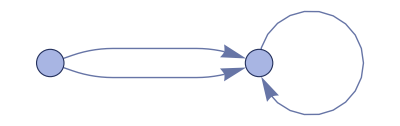

```mathematica
plot[wm[allRules[[2]], Automatic, steps, "FinalState"]]
```

Transpose::nmtx: The first two levels of … cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::nmtx: The first two levels of … cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

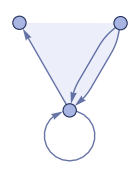
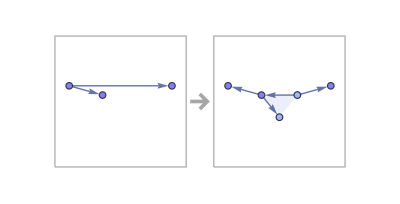
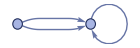
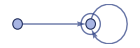
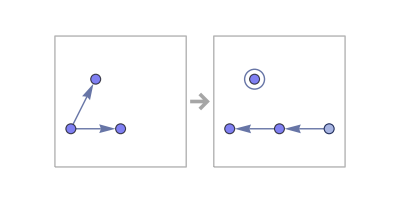
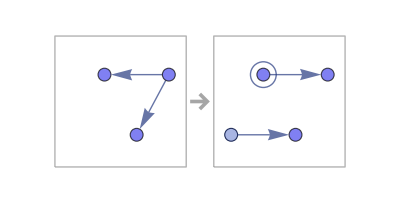
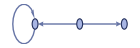
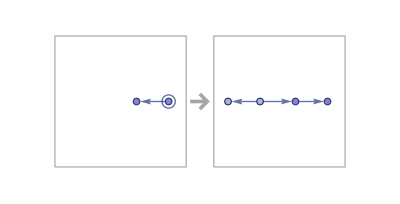
{-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

```mathematica
Labeled[Framed[ResourceFunction["WolframModelPlot"][ResourceFunction["WolframModel"][#,Automatic,steps,"FinalState"],ImageSize->140],FrameStyle->LightGray],RulePlot[ResourceFunction["WolframModel"][#],ImageSize->Tiny,"RulePartsAspectRatio"->1]]&/@allRules
```

```mathematica
GraphicsGrid[Partition[Labeled[Framed[ResourceFunction["WolframModelPlot"][ResourceFunction["WolframModel"][#,Automatic,steps,"FinalState"],ImageSize->140],FrameStyle->LightGray],RulePlot[ResourceFunction["WolframModel"][#],ImageSize->Tiny,"RulePartsAspectRatio"->1]]&/@allRules,3],ImageSize->Full,Alignment->Bottom]
```

Transpose::nmtx: The first two levels of … cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

Transpose::nmtx: The first two levels of … cannot be transposed.

Transpose::argt: Transpose called with 0 arguments; 1 or 2 arguments are expected.

-Graphics-

## Dimensionality

```mathematica
PairedDimension[{rule_,init_,steps_}]:=With[{wm=ResourceFunction["WolframModel"][rule,init,steps,"StatesList"]},GraphicsColumn[{ResourceFunction["WolframModelPlot"][Last[wm]],ListLinePlot[Select[Length[#]>3&]@(HypergraphDimensionEstimateList/@(If[Length[#]>20,Take[#,1;;-1;;Floor[Length[#]/20]],#]&@Select[wm,Length[#]>10&])),Frame->True,PlotRange->{0,Automatic},PlotStyle->ResourceFunction["WolframPhysicsProjectStyleData"]["GenericLinePlot","PlotStyles"]]},Frame->True,FrameStyle->LightGray]];
HypergraphDimensionEstimateList[hg_]:=ResourceFunction["LogDifferences"][MeanAround/@Transpose[Values[ResourceFunction["HypergraphNeighborhoodVolumes"][hg,All,Automatic]]]];
GraphicsGrid[Partition[ParallelMap[PairedDimension,{{{{x,y}}->{{x,z},{y,z},{z,z}},{{1,1}},5},{{{x,y}}->{{y,z},{y,w},{z,w},{z,x}},{{0,0}},6},{{{1,2,3}}->{{4,4,2},{4,1,3}},{{0,0,0}},10},{{{1,2},{1,3}}->{{1,4},{1,5},{2,4},{4,3},{5,3}},{{0,0},{0,0}},11},{{{1,2},{3,2}}->{{4,5},{4,1},{5,1},{5,2},{3,4}},{{0,0},{0,0}},11},{{{1,2},{1,3},{4,2}}->{{5,2},{5,2},{5,1},{5,4},{3,5}},{{0,0},{0,0},{0,0}},16},{{{1,2,3},{2,4,5}}->{{4,5,4},{5,6,1},{3,2,6}},{{0,0,0},{0,0,0}},18},{{{1,2},{1,3},{4,2}}->{{5,1},{5,1},{5,3},{5,4},{1,2}},{{0,0},{0,0},{0,0}},16},{{{1,2,3},{2,4,5}}->{{6,7,2},{5,7,8},{4,2,8},{9,3,5}},{{0,0,0},{0,0,0}},18},{{{1,2,3},{1,4,5}}->{{3,2,6},{2,5,6},{7,4,3},{1,8,7}},{{0,0,0},{0,0,0}},19},{{{1,2,3},{3,4}}->{{5,5,5},{5,6,4},{3,1},{1,5}},{{0,0,0},{0,0}},16},{{{1,2,3},{2,4}}->{{5,6,4},{4,1,6},{2,1},{3,6}},{{0,0,0},{0,0}},50}}],4],ImageSize->Full,Alignment->Bottom]
```

-Graphics-

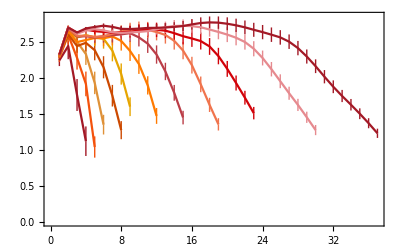

```mathematica
HypergraphDimensionEstimateList[hg_]:=ResourceFunction["LogDifferences"][MeanAround/@Transpose[Values[ResourceFunction["HypergraphNeighborhoodVolumes"][hg,All,Automatic]]]];
ListLinePlot[Select[Length[#]>3&][HypergraphDimensionEstimateList/@Drop[ResourceFunction["WolframModel"][{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{1,2},{1,3}},16,"StatesList"],4]],Frame->True,PlotStyle->ResourceFunction["WolframPhysicsProjectStyleData"]["GenericLinePlot","PlotStyles"]]
```

```mathematica
graph = ResourceFunction["WolframModel"][{{1,2},{3,2}}->{{4,5},{4,1},{5,1},{5,2},{3,4}},{{0,0},{0,0}},11, "FinalState"];
```

```mathematica
ResourceFunction["HypergraphNeighborhoodVolumes"][graph, All, Automatic];
```

```mathematica
HypergraphDimensionEstimateList[hg_]:=ResourceFunction["LogDifferences"][MeanAround/@Transpose[Values[ResourceFunction["HypergraphNeighborhoodVolumes"][hg,All,Automatic]]]];
```

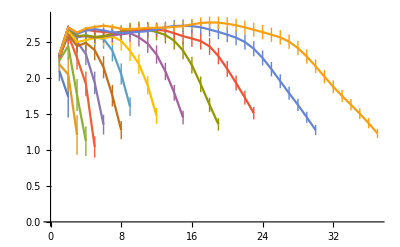

```mathematica
ListLinePlot[HypergraphDimensionEstimateList/@Drop[ResourceFunction["WolframModel"][{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}}, {{1,2},{1,3}},16,"StatesList"],4]]
```

```mathematica
g=final;
```

```mathematica
ResourceFunction["WolframHausdorffDimension"][g, All, "AllDimensions"]
```

[{{36,10},{20,3},{46,8},{32,47},{47,22},{22,15},{33,48},{48,23},{23,1},{34,49},{49,16},{16,14},{14,50},{50,1},{1,5},{35,51},{51,24},{24,5},{7,52},{52,5},{5,36},{10,53},{53,15},{15,11},{37,54},{54,25},{25,17},{38,55},{55,26},{26,18},{12,56},{56,18},{18,8},{39,57},{57,27},{27,19},{40,58},{58,28},{28,20},{41,59},{59,6},{6,3},{29,60},{60,3},{3,9},{42,61},{61,9},{9,13},{13,62},{62,19},{19,14},{43,63},{63,30},{30,1},{44,64},{64,21},{21,11},{11,65},{65,1},{1,4},{45,66},{66,31},{31,4},{2,67},{67,17},{17,46},{8,68},{68,4},{4,11}},All,AllDimensions]

```mathematica
g
```

{{36,10},{20,3},{46,8},{32,47},{47,22},{22,15},{33,48},{48,23},{23,1},{34,49},{49,16},{16,14},{14,50},{50,1},{1,5},{35,51},{51,24},{24,5},{7,52},{52,5},{5,36},{10,53},{53,15},{15,11},{37,54},{54,25},{25,17},{38,55},{55,26},{26,18},{12,56},{56,18},{18,8},{39,57},{57,27},{27,19},{40,58},{58,28},{28,20},{41,59},{59,6},{6,3},{29,60},{60,3},{3,9},{42,61},{61,9},{9,13},{13,62},{62,19},{19,14},{43,63},{63,30},{30,1},{44,64},{64,21},{21,11},{11,65},{65,1},{1,4},{45,66},{66,31},{31,4},{2,67},{67,17},{17,46},{8,68},{68,4},{4,11}}

```mathematica
ResourceFunction["WolframHausdorffDimension"][GridGraph[{20,20}], All, "AllDimensions"]
```

<|1→1.87042,2→1.79377,3→1.75956,4→1.74351,5→1.73659,6→1.73446,7→1.73469,8→1.73585,9→1.73707,10→1.7378,11→1.7378,12→1.73707,13→1.73585,14→1.73469,15→1.73446,16→1.73659,17→1.74351,18→1.75956,19→1.79377,20→1.87042,21→1.79377,22→1.71311,23→1.67686,24→1.6582,25→1.64879,26→1.64448,27→1.64297,28→1.64284,29→1.6432,30→1.64352,31→1.64352,32→1.6432,33→1.64284,34→1.64297,35→1.64448,36→1.64879,37→1.6582,38→1.67686,39→1.71311,40→1.79377,41→1.75956,42→1.67686,43→1.63518,44→1.6148,45→1.60377,46→1.59807,47→1.59543,48→1.59445,49→1.59426,50→1.59431,51→1.59431,52→1.59426,53→1.59445,54→1.59543,55→1.59807,56→1.60377,57→1.6148,58→1.63518,59→2.04238,60→2.18927,61→1.74351,62→1.6582,63→1.6148,64→1.58956,65→1.57728,66→1.57054,67→1.56707,68→1.56548,69→1.56489,70→1.56475,71→1.56475,72→1.56489,73→1.56548,74→1.56707,75→1.57054,76→1.57728,77→1.58956,78→1.87932,79→1.95535,80→2.09814,81→1.73659,82→1.64879,83→1.60377,84→1.57728,85→1.56077,86→1.55316,87→1.54903,88→1.54696,89→1.54606,90→1.54575,91→1.54575,92→1.54606,93→1.54696,94→1.54903,95→1.55316,96→1.56077,97→1.76207,98→1.81585,99→1.8874,100→2.02653,101→1.73446,102→1.64448,103→1.59807,104→1.57054,105→1.55316,106→1.54183,107→1.5371,108→1.53461,109→1.53344,110→1.533,111→1.533,112→1.53344,113→1.53461,114→1.5371,115→1.54183,116→1.67547,117→1.71563,118→1.76577,119→1.83211,120→1.96776,121→1.73469,122→1.64297,123→1.59543,124→1.56707,125→1.54903,126→1.5371,127→1.52901,128→1.52611,129→1.52468,130→1.52412,131→1.52412,132→1.52468,133→1.52611,134→1.52901,135→1.61147,136→1.6421,137→1.67926,138→1.72479,139→1.78532,140→1.91739,141→1.73585,142→1.64284,143→1.59445,144→1.56548,145→1.54696,146→1.53461,147→1.52611,148→1.5201,149→1.51839,150→1.51768,151→1.51768,152→1.51839,153→1.5201,154→1.56528,155→1.58855,156→1.61668,157→1.64988,158→1.68983,159→1.74386,160→1.87206,161→1.73707,162→1.6432,163→1.59426,164→1.56489,165→1.54606,166→1.53344,167→1.52468,168→1.51839,169→1.51374,170→1.51287,171→1.51287,172→1.51374,173→1.53388,174→1.55096,175→1.57214,176→1.59684,177→1.625,178→1.65853,179→1.70518,180→1.82905,181→1.7378,182→1.64352,183→1.59431,184→1.56475,185→1.54575,186→1.533,187→1.52412,188→1.51768,189→1.51287,190→1.50924,191→1.50924,192→1.51544,193→1.52684,194→1.54217,195→1.56036,196→1.5806,197→1.6026,198→1.62887,199→1.66698,200→1.78585,201→1.7378,202→1.64352,203→1.59431,204→1.56475,205→1.54575,206→1.533,207→1.52412,208→1.51768,209→1.51287,210→1.50924,211→1.50924,212→1.51493,213→1.5248,214→1.53745,215→1.55164,216→1.56622,217→1.58105,218→1.59896,219→1.62704,220→1.74002,221→1.73707,222→1.6432,223→1.59426,224→1.56489,225→1.54606,226→1.53344,227→1.52468,228→1.51839,229→1.51374,230→1.51544,231→1.51493,232→1.51917,233→1.52655,234→1.5355,235→1.54451,236→1.55211,237→1.55868,238→1.56677,239→1.58272,240→1.68884,241→1.73585,242→1.64284,243→1.59445,244→1.56548,245→1.54696,246→1.53461,247→1.52611,248→1.5201,249→1.53388,250→1.52684,251→1.5248,252→1.52655,253→1.53034,254→1.53436,255→1.53665,256→1.53584,257→1.53247,258→1.5287,259→1.53057,260→1.6294,261→1.73469,262→1.64297,263→1.59543,264→1.56707,265→1.54903,266→1.5371,267→1.52901,268→1.56528,269→1.55096,270→1.54217,271→1.53745,272→1.5355,273→1.53436,274→1.53181,275→1.52546,276→1.51451,277→1.49969,278→1.48292,279→1.46958,280→1.56056,281→1.73446,282→1.64448,283→1.59807,284→1.57054,285→1.55316,286→1.54183,287→1.61147,288→1.58855,289→1.57214,290→1.56036,291→1.55164,292→1.54451,293→1.53665,294→1.52546,295→1.50892,296→1.48685,297→1.45968,298→1.42884,299→1.39888,300→1.48138,301→1.73659,302→1.64879,303→1.60377,304→1.57728,305→1.56077,306→1.67547,307→1.6421,308→1.61668,309→1.59684,310→1.5806,311→1.56622,312→1.55211,313→1.53584,314→1.51451,315→1.48685,316→1.45267,317→1.41201,318→1.36576,319→1.31745,320→1.39077,321→1.74351,322→1.6582,323→1.6148,324→1.58956,325→1.76207,326→1.71563,327→1.67926,328→1.64988,329→1.625,330→1.6026,331→1.58105,332→1.55868,333→1.53247,334→1.49969,335→1.45968,336→1.41201,337→1.35637,338→1.29298,339→1.22411,340→1.28745,341→1.75956,342→1.67686,343→1.63518,344→1.87932,345→1.81585,346→1.76577,347→1.72479,348→1.68983,349→1.65853,350→1.62887,351→1.59896,352→1.56677,353→1.5287,354→1.48292,355→1.42884,356→1.36576,357→1.29298,358→1.20997,359→1.11751,360→1.17001,361→1.79377,362→1.71311,363→2.04238,364→1.95535,365→1.8874,366→1.83211,367→1.78532,368→1.74386,369→1.70518,370→1.66698,371→1.62704,372→1.58272,373→1.53057,374→1.46958,375→1.39888,376→1.31745,377→1.22411,378→1.11751,379→0.996657,380→1.03764,381→1.87042,382→2.2878,383→2.16455,384→2.07217,385→1.99885,386→1.93786,387→1.88468,388→1.83587,389→1.78855,390→1.74002,391→1.68749,392→1.62776,393→1.5585,394→1.47874,395→1.38723,396→1.28245,397→1.1624,398→1.0245,399→0.865397,400→1.87042|>

```mathematica
g
```

{{36,10},{20,3},{46,8},{32,47},{47,22},{22,15},{33,48},{48,23},{23,1},{34,49},{49,16},{16,14},{14,50},{50,1},{1,5},{35,51},{51,24},{24,5},{7,52},{52,5},{5,36},{10,53},{53,15},{15,11},{37,54},{54,25},{25,17},{38,55},{55,26},{26,18},{12,56},{56,18},{18,8},{39,57},{57,27},{27,19},{40,58},{58,28},{28,20},{41,59},{59,6},{6,3},{29,60},{60,3},{3,9},{42,61},{61,9},{9,13},{13,62},{62,19},{19,14},{43,63},{63,30},{30,1},{44,64},{64,21},{21,11},{11,65},{65,1},{1,4},{45,66},{66,31},{31,4},{2,67},{67,17},{17,46},{8,68},{68,4},{4,11}}

```mathematica
ResourceFunction["WolframHausdorffDimension"][Graph@g, All, "VertexMethod"->#]&/@{Max,Min,Mean}
```

{2.16982,1.22743,1.69652}

```mathematica
ResourceFunction["WolframHausdorffDimension"][GridGraph[{10,10}], All, "VertexMethod"->#]&/@{Max,Min,Mean}
```

{2.05805,1.24891,1.61878}

```mathematica
TripledDimension[{rule_, init_, steps_}] :=
  	With[{wm = ResourceFunction["WolframModel"][rule, init, steps, "StatesList"]},
   		GraphicsColumn[{ResourceFunction["WolframModelPlot"][Last[wm]],
		ListLinePlot[Select[Length[#] > 3 &]@(HypergraphDimensionEstimateList /@ (If[Length[#] > 20, Take[#, 1 ;; -1 ;; Floor[Length[#]/20]], #] &@Select[wm, Length[#] > 10 &])), Frame -> True, PlotRange -> {0, Automatic}, PlotStyle -> ResourceFunction["WolframPhysicsProjectStyleData"]["GenericLinePlot", "PlotStyles"]],

     		Text[(N[ResourceFunction["WolframHausdorffDimension"][ResourceFunction["HypergraphToGraph"][Last[wm]], All, "VertexMethod" -> #], 2])&/@{Min,Mean,Max}]}, Frame -> True, FrameStyle -> LightGray]];
		
HypergraphDimensionEstimateList[hg_] := ResourceFunction["LogDifferences"][MeanAround /@ Transpose[Values[ResourceFunction["HypergraphNeighborhoodVolumes"][hg, All, Automatic]]]];
GraphicsGrid[Partition[ParallelMap[TripledDimension, {{{{x, y}} -> {{x, z}, {y, z}, {z, z}}, {{1, 1}}, 5}, {{{x, y}} -> {{y, z}, {y, w}, {z, w}, {z, x}}, {{0, 0}}, 6}, {{{1, 2, 3}} -> {{4, 4, 2}, {4, 1, 3}}, {{0, 0, 0}}, 10}, {{{1, 2}, {1, 3}} -> {{1, 4}, {1, 5}, {2, 4}, {4, 3}, {5, 3}}, {{0, 0}, {0, 0}}, 11}, {{{1, 2}, {3, 2}} -> {{4, 5}, {4, 1}, {5, 1}, {5, 2}, {3, 4}}, {{0, 0}, {0, 0}}, 11}, {{{1, 2}, {1, 3}, {4, 2}} -> {{5, 2}, {5, 2}, {5, 1}, {5, 4}, {3, 5}}, {{0, 0}, {0, 0}, {0, 0}}, 16}, {{{1, 2, 3}, {2, 4, 5}} -> {{4, 5, 4}, {5, 6, 1}, {3, 2, 6}}, {{0, 0, 0}, {0, 0, 0}}, 18}, {{{1, 2}, {1, 3}, {4, 2}} -> {{5, 1}, {5, 1}, {5, 3}, {5, 4}, {1, 2}}, {{0, 0}, {0, 0}, {0, 0}}, 16}, {{{1, 2, 3}, {2, 4, 5}} -> {{6, 7, 2}, {5, 7, 8}, {4, 2, 8}, {9, 3, 5}}, {{0, 0, 0}, {0, 0, 0}}, 18}, {{{1, 2, 3}, {1, 4, 5}} -> {{3, 2, 6}, {2, 5, 6}, {7, 4, 3}, {1, 8, 7}}, {{0, 0, 0}, {0, 0, 0}}, 19}, {{{1, 2, 3}, {3, 4}} -> {{5, 5, 5}, {5, 6, 4}, {3, 1}, {1, 5}}, {{0, 0, 0}, {0, 0}}, 16}, {{{1, 2, 3}, {2, 4}} -> {{5, 6, 4}, {4, 1, 6}, {2, 1}, {3, 6}}, {{0, 0, 0}, {0, 0}}, 50}}], 4], ImageSize -> Full, Alignment -> Bottom]
```

ParallelMap::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelMap::subpar will be suppressed during this calculation.

ParallelMap::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelMap::subpar will be suppressed during this calculation.

ParallelMap::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelMap::subpar will be suppressed during this calculation.

ParallelMap::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelMap::subpar will be suppressed during this calculation.

ParallelMap::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelMap::subpar will be suppressed during this calculation.

ParallelMap::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelMap::subpar will be suppressed during this calculation.

ParallelMap::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

General::stop: Further output of ParallelMap::subpar will be suppressed during this calculation.

-Graphics-

```mathematica
wm=ResourceFunction["WolframModel"][{{x,y}}->{{x,y},{x,z},{y,z}}, {{0,0}}, 5, "FinalState"]
```

{{0,0},{0,41},{0,41},{0,14},{0,42},{14,42},{0,14},{0,43},{14,43},{0,5},{0,44},{5,44},{0,15},{0,45},{15,45},{5,15},{5,46},{15,46},{0,5},{0,47},{5,47},{0,16},{0,48},{16,48},{5,16},{5,49},{16,49},{0,2},{0,50},{2,50},{0,17},{0,51},{17,51},{2,17},{2,52},{17,52},{0,6},{0,53},{6,53},{0,18},{0,54},{18,54},{6,18},{6,55},{18,55},{2,6},{2,56},{6,56},{2,19},{2,57},{19,57},{6,19},{6,58},{19,58},{0,2},{0,59},{2,59},{0,20},{0,60},{20,60},{2,20},{2,61},{20,61},{0,7},{0,62},{7,62},{0,21},{0,63},{21,63},{7,21},{7,64},{21,64},{2,7},{2,65},{7,65},{2,22},{2,66},{22,66},{7,22},{7,67},{22,67},{0,1},{0,68},{1,68},{0,23},{0,69},{23,69},{1,23},{1,70},{23,70},{0,8},{0,71},{8,71},{0,24},{0,72},{24,72},{8,24},{8,73},{24,73},{1,8},{1,74},{8,74},{1,25},{1,75},{25,75},{8,25},{8,76},{25,76},{0,3},{0,77},{3,77},{0,26},{0,78},{26,78},{3,26},{3,79},{26,79},{0,9},{0,80},{9,80},{0,27},{0,81},{27,81},{9,27},{9,82},{27,82},{3,9},{3,83},{9,83},{3,28},{3,84},{28,84},{9,28},{9,85},{28,85},{1,3},{1,86},{3,86},{1,29},{1,87},{29,87},{3,29},{3,88},{29,88},{1,10},{1,89},{10,89},{1,30},{1,90},{30,90},{10,30},{10,91},{30,91},{3,10},{3,92},{10,92},{3,31},{3,93},{31,93},{10,31},{10,94},{31,94},{0,1},{0,95},{1,95},{0,32},{0,96},{32,96},{1,32},{1,97},{32,97},{0,11},{0,98},{11,98},{0,33},{0,99},{33,99},{11,33},{11,100},{33,100},{1,11},{1,101},{11,101},{1,34},{1,102},{34,102},{11,34},{11,103},{34,103},{0,4},{0,104},{4,104},{0,35},{0,105},{35,105},{4,35},{4,106},{35,106},{0,12},{0,107},{12,107},{0,36},{0,108},{36,108},{12,36},{12,109},{36,109},{4,12},{4,110},{12,110},{4,37},{4,111},{37,111},{12,37},{12,112},{37,112},{1,4},{1,113},{4,113},{1,38},{1,114},{38,114},{4,38},{4,115},{38,115},{1,13},{1,116},{13,116},{1,39},{1,117},{39,117},{13,39},{13,118},{39,118},{4,13},{4,119},{13,119},{4,40},{4,120},{40,120},{13,40},{13,121},{40,121}}

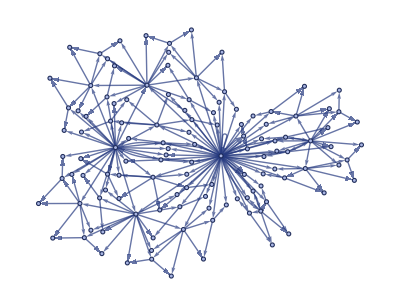

```mathematica
ResourceFunction["WolframModelPlot"][wm]
```

```mathematica
ResourceFunction["WolframHausdorffDimension"][wm, All, "VertexMethod"->Max]
```

[{{0,0},{0,41},{0,41},{0,14},{0,42},{14,42},{0,14},{0,43},{14,43},{0,5},{0,44},{5,44},{0,15},{0,45},{15,45},{5,15},{5,46},{15,46},{0,5},{0,47},{5,47},{0,16},{0,48},{16,48},{5,16},{5,49},{16,49},{0,2},{0,50},{2,50},{0,17},{0,51},{17,51},{2,17},{2,52},{17,52},{0,6},{0,53},{6,53},{0,18},{0,54},{18,54},{6,18},{6,55},{18,55},{2,6},{2,56},{6,56},{2,19},{2,57},{19,57},{6,19},{6,58},{19,58},{0,2},{0,59},{2,59},{0,20},{0,60},{20,60},{2,20},{2,61},{20,61},{0,7},{0,62},{7,62},{0,21},{0,63},{21,63},{7,21},{7,64},{21,64},{2,7},{2,65},{7,65},{2,22},{2,66},{22,66},{7,22},{7,67},{22,67},{0,1},{0,68},{1,68},{0,23},{0,69},{23,69},{1,23},{1,70},{23,70},{0,8},{0,71},{8,71},{0,24},{0,72},{24,72},{8,24},{8,73},{24,73},{1,8},{1,74},{8,74},{1,25},{1,75},{25,75},{8,25},{8,76},{25,76},{0,3},{0,77},{3,77},{0,26},{0,78},{26,78},{3,26},{3,79},{26,79},{0,9},{0,80},{9,80},{0,27},{0,81},{27,81},{9,27},{9,82},{27,82},{3,9},{3,83},{9,83},{3,28},{3,84},{28,84},{9,28},{9,85},{28,85},{1,3},{1,86},{3,86},{1,29},{1,87},{29,87},{3,29},{3,88},{29,88},{1,10},{1,89},{10,89},{1,30},{1,90},{30,90},{10,30},{10,91},{30,91},{3,10},{3,92},{10,92},{3,31},{3,93},{31,93},{10,31},{10,94},{31,94},{0,1},{0,95},{1,95},{0,32},{0,96},{32,96},{1,32},{1,97},{32,97},{0,11},{0,98},{11,98},{0,33},{0,99},{33,99},{11,33},{11,100},{33,100},{1,11},{1,101},{11,101},{1,34},{1,102},{34,102},{11,34},{11,103},{34,103},{0,4},{0,104},{4,104},{0,35},{0,105},{35,105},{4,35},{4,106},{35,106},{0,12},{0,107},{12,107},{0,36},{0,108},{36,108},{12,36},{12,109},{36,109},{4,12},{4,110},{12,110},{4,37},{4,111},{37,111},{12,37},{12,112},{37,112},{1,4},{1,113},{4,113},{1,38},{1,114},{38,114},{4,38},{4,115},{38,115},{1,13},{1,116},{13,116},{1,39},{1,117},{39,117},{13,39},{13,118},{39,118},{4,13},{4,119},{13,119},{4,40},{4,120},{40,120},{13,40},{13,121},{40,121}},All,VertexMethod→Max]

```mathematica
ResourceFunction["HypergraphToGraph"][wm]
```

-Graphics-

```mathematica
ResourceFunction["WolframHausdorffDimension"][ResourceFunction["HypergraphToGraph"][wm], All, "VertexMethod"->Max]
```

2.57518

```mathematica
AgeHypergraphPlot[evolutionObject_,gradientList_:{Red,Blue},exp_:.25]:=With[{totalGenerationsCount=evolutionObject["TotalGenerationsCount"]},ResourceFunction["WolframModelPlot"][evolutionObject[-1],EdgeStyle->Association[MapThread[#1->Directive[Thick,Opacity[.9],Blend[gradientList,1-Exp[exp (#2-totalGenerationsCount)]]]&,{evolutionObject["AllExpressions"],evolutionObject["ExpressionGenerations"]}]],VertexSize->0,VertexStyle->Transparent]];
AgeHypergraphPlot[ResourceFunction["WolframModel"][#,{{0,0,0},{0,0,0}},500],{Hue[1,0.81,0.89],Hue[0.5700000000000001,0.16,0.86],Hue[0.59,0.15,0.89]},.0018]&/@{{{1,2,2},{3,1,4}}->{{2,5,2},{2,3,5},{4,5,5}},{{1,1,2},{1,3,4}}->{{4,4,3},{2,5,3},{2,5,3}},{{1,1,2},{1,3,4}}->{{4,4,5},{5,4,2},{3,2,5}},{{1,2,1},{1,3,4}}->{{4,5,4},{5,4,3},{1,2,5}}}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

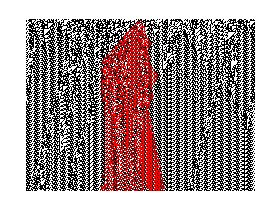
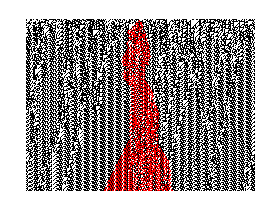

```mathematica
SeedRandom[24246];Table[With[{u=RandomInteger[1,400]},ArrayPlot[Sum[(2+(-1)^i) CellularAutomaton[110,ReplacePart[u,200->i],300],{i,0,1}],ColorRules->{0->White,4->Black,1->Red,3->Red},ImageSize->280]],2]
```

## Replacements based on graph replacements

#### Some weird meta stuff going on

Apply different possible replacements from wolfram models to wolfram model rules

Possibility for recursion

Probably be able to generate the whole universe

Have to choose which paths to go down based on desired behavior